D:\VELA\GIT Projects\Software\Apps\RF_Conditioner\logs\data

```mathematica
typemap=<|"<enum 'ramp_method'>"->"Byte","<type 'numpy.float64'>"->"Real64","<enum 'state'>"->"Byte","<class 'VELA_CLARA_enums.STATE'>"->"Byte","<class 'VELA_CLARA_RF_Modulator_Control.GUN_MOD_STATE'>"->"Byte","<class 'VELA_CLARA_RF_Protection_Control.RF_GUN_PROT_STATUS'>"->"Byte","<class 'VELA_CLARA_Vac_Valve_Control.VALVE_STATE'>"->"Byte","<type 'bool'>"->"Byte","<type 'float'>"->"Real32","<type 'int'>"->"Integer32","<type 'long'>"->"Integer32","<class 'VELA_CLARA_LLRF_Control.TRIG'>"->"Byte","<class 'VELA_CLARA_LLRF_Control.INTERLOCK_STATE'>"->"Byte","<class 'VELA_CLARA_RF_Protection_Control.RF_PROT_STATUS'>"->"Byte"|>;
```

```mathematica
FileNames[]
```

{2020-08-04-13-51-54,data_log,data_log_read_multifile_20200804.nb}

```mathematica
SetDirectory[NotebookDirectory[]];
file="data_log";
str=OpenRead[file,BinaryFormat->True];
heads=StringSplit[ReadLine[str],"\t"];
types=StringSplit[ReadLine[str],"\t"];
BinaryRead[str,{"Character8"}]
data=BinaryReadList[str,Lookup[typemap,types]];
Close[str];
Transpose[{heads,data⟦120⟧}]//TableForm
```

{\r}

p0_all | -4.36718×10^130
llrf_output_status | 64
next_sp_decrease | -2.21485×10^14
probe_pha | -1.53955
rev_cav_pha | 2450.
can_llrf_output_state_OLD | 1
breakdown_rate_aim | 1190716675
phi_sp | 1770062337
num_outside_mask_traces | 524135
next_requested_power_change | 851968
modulator_good | 0
p2_current_sp_to_fit | -1.35326×10^-24
CAVITY_TEMP_ID_0 | 1.18759×10^28
p2_current_sp | 2.03222
pulse_length_status | 28
pulse_length | 1843782086
llrf_trace_interlock | 67
cav_pwr_ratio_good | 1
llrf_interlock | 1
SP_QUAD_ALL | 2939.
water_temp_gui | -0.000156056
last_requested_power_change | -1014497284
max_sp_increase | 5.86054×10^-35
ramp_mode | 0
llrf_ff_ph_locked | 0
rev_kly_pha | 1.81936×10^-38
llrf_ff_amp_locked_status | 96
pulse_length_min | 16860474
llrf_DAQ_rep_rate_status_previous | 1
delta_kfpow | 1.76412×10^23
llrf_trigger | 198
cav_pwr_ratio_can_ramp | 54
p1_current_sp_to_fit | 5.10559×10^-137
vac_level | -3.85167×10^-34
gui_can_rf_output | 195
can_rf_output_status_OLD | 192
bd_rate_calc_first_pulse_number | 432639
pulse_length_max | 2573
cav_pwr_ratio | -1.4412×10^17
number_of_pulses_in_breakdown_history | 2130790274
probe_outside_mask_count | -1586242272
llrf_interlock_status | 45
current_ramp_index | 17416404
y_min | 8.12211×10^-252
old_x_min | 0.
old_x_max | 8.18144×10^-36
rev_kly_pwr | 230877.
fwd_kly_pha | -6.42722×10^-22
active_breakdown_count | 1220673542
last_sp_above_100 | 1.08654×10^-19
event_pulse_count | -1436203716
time_stamp, (start = 2020-08-04 13:52:18.463000) | 2.00403
log_ramp_curve_index | 16893468
TOR_SCAN | 1024148374
llrf_ff_ph_locked_status | 13
last_mean_power | -0.000260328
rev_cav_pwr | 5.19882×10^-43
SP_QUAD_CURRENT_SP_TO_FIT | 1.94945×10^25
last_vac_spike_status | 103
llrf_DAQ_rep_rate_status | 255
x_max | 9.21956×10^-41
p0_current_sp_to_fit | 1.0842×10^-19
amp_ff | 1734967621
c | 1.24361619×10^-314
L01-SOL1 | -7.69038×10^36
L01-SOL2 | -6.11035
y_max | -6.27173×10^292
p1_current_sp | 7.68821×10^9
x_min | -7.81731×10^9
can_ramp_status | 161
kfpower_at_last_amp_sp | 3.51557×10^-38
vac_level_can_ramp | 0
last_breakdown_status | 64
reverse_outside_mask_count | 1073792540
llrf_DAQ_rep_rate_min | 1662174748
llrf_DAQ_rep_rate_max | 1677804389
TOR_ACQM | -318767104
p0_current_sp | -9.12488×10^192
breakdown_rate_low | 3
WATER_TEMP_ID_1 | 2.61643×10^33
cav_temp | 5.18877×10^-20
fwd_cav_pha | 5.66382×10^22
BD_state_OLD | 170
rfprot_good | 252
last_amp_sp | -2.15288×10^-10
vac_spike_status | 142
old_y_max | 1.35427734502597×10^-308
event_pulse_count_zero | 256
DC_level | 2941.
amp_sp | 31.5832
global_mask_checking | 0
gui_can_ramp | 0
can_llrf_output_state | 0
p1_all | 9.307×10^245
expected_pulse_length | 21211043
old_y_min | 2.46437×10^-285
log_pulse_count | 1593901380
llrf_DAQ_rep_rate_aim | 1337364581
llrf_ff_amp_locked | 213
catap_max_amp | -1.97877×10^28
can_ramp_status_OLD | 25
p2_all | -1.61052×10^265
fwd_kly_pwr | 1.51116×10^23
sol_value | 2.97043
log_amp_set | -2130702526
duplicate_pulse_count | 33515369
m | 4.6938×10^61
pulse_count | 1087711251
fwd_cav_pwr | -10000.
SP_SLF | -10000.
WATER_TEMP_ID_0 | 100.249
probe_pwr | 172.096
llrf_output | 0
can_rf_output_status | 0
log_pulse_length | 2.
modulator_state | 28
elapsed_time | 32710
DC_spike_status | 0
llrf_trigger_status | 0
pulses_to_next_ramp | 12983360
GUI_mod_and_prot_good | 0
breakdown_status | 0
catap_max_amp_can_ramp_status | 0
main_can_ramp | 2
llrf_DAQ_rep_rate | 2.35099×10^-38
vac_valve_status | 0
SP_QUAD_CURRENT | -3.21452×10^34
rev_power_spike_count | 4326167
BD_state | 96
last_ramp_method | 58
required_pulses | 66117
rfprot_state | 224
old_m | 1.77312×10^-89
total_breakdown_count | 1770078065
old_c | -8.05758×10^-255
cav_temp_gui | Indeterminate

```mathematica
data⟦1⟧
```

{-3.78425×10^-270,195,2.00011,2.01209,-1.08885×10^18,228,6554178,-1245184,65535,1770061824,103,-3.78425×10^-270,2.01177,-3.78425×10^-270,195,163381696,0,0,1,2.,-1.68168×10^12,1770078716,2.01559,28,198,-0.000123061,230,-1845411053,9,-2.93312×10^-11,56,37,Indeterminate,8.16386×10^-20,111,20,-1090387664,-150997161,-9.67142×10^24,1119619597,1000000,129,33515369,-6.27173×10^292,-6.11035,-10000.,-10000.,0.940188,1125620226,0.,-971227136,0.,-971227136,-9999999,2,2.35099×10^-38,-10000.,2.2095,0,64,2.40194×10^-38,-6.27173×10^292,-1060927489,-6.27173×10^292,-6.11035,-999.999,-6.27173×10^292,-6.27173×10^292,-6.11035,0,2.91097×10^-37,0,64,33670684,-9999999,7,13,-6.27173×10^292,255,7.08102×10^-38,31.6929,-10000.,181,237,2.39254×10^-38,0,-6.27173×10^292,-1060927489,6.06256×10^-40,-10000.,0,0,0,-6.27173×10^292,-1060927489,-6.27173×10^292,-1060927489,432639,13,1.4013×10^-44,1,-1.89095×10^-33,-272.,-1.12175×10^-21,473956415,773574,-1.89095×10^-33,-1014497284,5.7928×10^-35,1.86165×10^-25,6.35278×10^-22,-8.79636×10^36,65,0,7.27742×10^-38,2,1024148374,13,237,1941538713,1,0,0,2,1.10269×10^24,255,9.21942×10^-41,1092692619,1,0,-2117723072,105,3.1829946571×10^-312,-1188846848,4.090439594×10^-312,-0.000156056}

## Concatenating Data Logs

```mathematica
FastListPlot[data_,opts:OptionsPattern[]]:=Module[{interp},interp=Interpolation[data];
Plot[interp[x],{x,interp[[1,1,1]],interp[[1,1,2]]},opts]]
```

```mathematica
getDataLog[fn_]:=Block[{file=fn,str,heads,types,data,typemap=<|"<class 'VELA_CLARA_enums.STATE'>"->"Byte","<class 'VELA_CLARA_RF_Modulator_Control.GUN_MOD_STATE'>"->"Byte",
"<class 'VELA_CLARA_LLRF_Control.INTERLOCK_STATE'>"->"Byte","<class 'VELA_CLARA_LLRF_Control.TRIG'>"->"Byte","<class 'VELA_CLARA_RF_Protection_Control.RF_PROT_STATUS'>"->"Byte","<class 'VELA_CLARA_RF_Protection_Control.RF_GUN_PROT_STATUS'>"->"Byte","<class 'VELA_CLARA_Vac_Valve_Control.VALVE_STATE'>"->"Byte","<type 'bool'>"->"Byte","<type 'float'>"->"Real32","<type 'int'>"->"Integer32","<type 'long'>"->"Integer32","<enum 'state'>"->"Byte"|>,data2,timestamp,ts},
str=OpenRead[file,BinaryFormat->True];
heads=StringSplit[ReadLine[str],"\t"];
types=StringSplit[ReadLine[str],"\t"];
BinaryRead[str,{"Character8"}];
data=BinaryReadList[str,Lookup[typemap,types]];
Close[str];
data2=data;
(* Now we offset the timestamp column to be in seconds since the epoch... *)
timestamp=Position[StringContainsQ[heads,"time_stamp"],True];
ts=AbsoluteTime[DateObject[StringTake[Extract[heads,timestamp]⟦1⟧,{22,-4}]]];
data2⟦All,timestamp⟦1⟧⟧=Flatten[data2⟦All,timestamp⟦1⟧⟧+ts];
{heads,data2}
]
```

```mathematica
PrimeQ[53257]
PrimeQ[23571113172329313753257]
```

False

True

```mathematica
(2 10^6)/60.
```

33333.3

## many files

```mathematica
directoryroot="C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\Breakdowns";
SetDirectory[directoryroot];
datadirs=Select[FileNames[],DirectoryQ@#&]
```

{Binary_log,ML,outside_forward,outside_reverse}

SetDirectory::cdir: Cannot set current directory to C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\Breakdowns\Binary_log\data_log.

{ABViewer 14,AllTraces,Appraisals,AP_RF_Lecture_notes,Bead_Pull,Cern,Cockroft Institute Lectures,Covid-19,CST,Custom Office Templates,ESS,Git,GPC,gun_10_csv_data,Gun_10_Upgrade,High Power RF Test Area,Induction,IPAC,Mathematica,Mechanical_Drawings,MSc JBCA,OneNote Notebooks,Oracle,Papers,Study Material,Training,USPAS,Wolfram Mathematica,XFEL,Zoom}

```mathematica
(*get folders adn files that contain this string *)
lfstring=".dat";
datafiles=FileNameJoin[{directoryroot,#⟦1⟧,#⟦2,1⟧}]&/@Select[Table[
SetDirectory[FileNameJoin[{directoryroot,datadirs⟦i⟧}]];
{datadirs⟦i⟧,Select[FileNames[],StringContainsQ[#,lfstring]&]}
,{i,1,Length@datadirs}],Length@#⟦2⟧>0&];
```

SetDirectory::cdir: Cannot set current directory to C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\Breakdowns\Binary_log\data_log\ABViewer 14.

SetDirectory::cdir: Cannot set current directory to C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\Breakdowns\Binary_log\data_log\AllTraces.

SetDirectory::cdir: Cannot set current directory to C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\Breakdowns\Binary_log\data_log\Appraisals.

General::stop: Further output of SetDirectory::cdir will be suppressed during this calculation.

```mathematica
Speak[lfstring=".dat";]
```

```mathematica
td=getDataLog[#]&/@datafiles;
```

```mathematica
Transpose[{td⟦1,1⟧,Range@Length@td⟦1,1⟧}]
```

{{llrf_DAQ_rep_rate_min,1},{phi_sp,2},{x_max,3},{next_sp_decrease,4},{probe_pha,5},{rev_cav_pha,6},{llrf_DAQ_rep_rate_max,7},{TOR_ACQM,8},{breakdown_rate_aim,9},{llrf_output_status,10},{num_outside_mask_traces,11},{cav_temp,12},{fwd_cav_pha,13},{pulse_length_status,14},{pulse_length,15},{llrf_interlock,16},{last_106_bd_count,17},{pulse_length_aim,18},{breakdown_rate_hi,19},{amp_sp,20},{PID_on_off,21},{max_sp_increase,22},{old_y_max,23},{llrf_ff_ph_locked,24},{rev_kly_pha,25},{vac_val_limit,26},{breakdown_rate,27},{vac_spike_status,28},{next_power_increase,29},{water_temp,30},{pulse_length_min,31},{vac_valve_status,32},{pulse_length_aim_error,33},{llrf_trigger_status,34},{log_pulse_count,35},{llrf_trigger,36},{llrf_DAQ_rep_rate_aim,37},{power_aim,38},{vac_level,39},{llrf_DAQ_rep_rate_status_previous,40},{phase_mask_by_power_trace_2_set,41},{y_min,42},{rev_power_spike_count,43},{phase_end_mask_by_power_trace_2_time,44},{fwd_kly_pwr,45},{breakdown_count,46},{probe_pwr,47},{log_amp_set,48},{duplicate_pulse_count,49},{pulse_length_max,50},{phase_mask_by_power_trace_1_set,51},{pulse_count,52},{fwd_cav_pwr,53},{llrf_ff_amp_locked_status,54},{sol_value,55},{llrf_output,56},{DC_level,57},{llrf_interlock_status,58},{current_ramp_index,59},{log_pulse_length,60},{old_x_min,61},{modulator_state,62},{llrf_ff_amp_locked,63},{old_x_max,64},{phase_end_mask_by_power_trace_1_time,65},{elapsed_time,66},{rev_kly_pwr,67},{DC_spike_status,68},{fwd_kly_pha,69},{last_sp_above_100,70},{event_pulse_count,71},{time_stamp, (start = 2019-12-04 17:50:42.185000),72},{TOR_SCAN,73},{llrf_ff_ph_locked_status,74},{last_mean_power,75},{rev_cav_pwr,76},{x_min,77},{old_y_min,78},{llrf_DAQ_rep_rate_status,79},{can_rf_output,80},{llrf_DAQ_rep_rate,81},{c,82},{y_max,83},{m,84},{breakdown_status,85},{required_pulses,86},{rfprot_state,87},{old_m,88},{old_c,89},{can_rf_output_OLD,90}}

```mathematica
{{"llrf_DAQ_rep_rate_min",1},{"phi_sp",2},{"x_max",3},{"next_sp_decrease",4},{"probe_pha",5},{"rev_cav_pha",6},{"llrf_DAQ_rep_rate_max",7},{"TOR_ACQM",8},{"breakdown_rate_aim",9},{"llrf_output_status",10},{"num_outside_mask_traces",11},{"cav_temp",12},{"fwd_cav_pha",13},{"pulse_length_status",14},{"pulse_length",15},{"llrf_interlock",16},{"last_106_bd_count",17},{"pulse_length_aim",18},{"breakdown_rate_hi",19},{"amp_sp",20},{"PID_on_off",21},{"max_sp_increase",22},{"old_y_max",23},{"llrf_ff_ph_locked",24},{"rev_kly_pha",25},{"vac_val_limit",26},{"breakdown_rate",27},{"vac_spike_status",28},{"next_power_increase",29},{"water_temp",30},{"pulse_length_min",31},{"vac_valve_status",32},{"pulse_length_aim_error",33},{"llrf_trigger_status",34},{"log_pulse_count",35},{"llrf_trigger",36},{"llrf_DAQ_rep_rate_aim",37},{"power_aim",38},{"vac_level",39},{"llrf_DAQ_rep_rate_status_previous",40},{"phase_mask_by_power_trace_2_set",41},{"y_min",42},{"rev_power_spike_count",43},{"phase_end_mask_by_power_trace_2_time",44},{"fwd_kly_pwr",45},{"breakdown_count",46},{"probe_pwr",47},{"log_amp_set",48},{"duplicate_pulse_count",49},{"pulse_length_max",50},{"phase_mask_by_power_trace_1_set",51},{"pulse_count",52},{"fwd_cav_pwr",53},{"llrf_ff_amp_locked_status",54},{"sol_value",55},{"llrf_output",56},{"DC_level",57},{"llrf_interlock_status",58},{"current_ramp_index",59},{"log_pulse_length",60},{"old_x_min",61},{"modulator_state",62},{"llrf_ff_amp_locked",63},{"old_x_max",64},{"phase_end_mask_by_power_trace_1_time",65},{"elapsed_time",66},{"rev_kly_pwr",67},{"DC_spike_status",68},{"fwd_kly_pha",69},{"last_sp_above_100",70},{"event_pulse_count",71},{"time_stamp, (start = 2019-12-04 17:50:42.185000)",72},{"TOR_SCAN",73},{"llrf_ff_ph_locked_status",74},{"last_mean_power",75},{"rev_cav_pwr",76},{"x_min",77},{"old_y_min",78},{"llrf_DAQ_rep_rate_status",79},{"can_rf_output",80},{"llrf_DAQ_rep_rate",81},{"c",82},{"y_max",83},{"m",84},{"breakdown_status",85},{"required_pulses",86},{"rfprot_state",87},{"old_m",88},{"old_c",89},{"can_rf_output_OLD",90}}


DuplicatePulseCount=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,49⟧}],{i,1,Length@td}]],2];
DuplicatePulseCount0=Transpose[{DuplicatePulseCount⟦All,1⟧-DuplicatePulseCount⟦1,1⟧,DuplicatePulseCount⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\DuplicatePulseCount_Data.csv",DuplicatePulseCount0,"Table"]
```

{{llrf_DAQ_rep_rate_min,1},{phi_sp,2},{x_max,3},{next_sp_decrease,4},{probe_pha,5},{rev_cav_pha,6},{llrf_DAQ_rep_rate_max,7},{TOR_ACQM,8},{breakdown_rate_aim,9},{llrf_output_status,10},{num_outside_mask_traces,11},{cav_temp,12},{fwd_cav_pha,13},{pulse_length_status,14},{pulse_length,15},{llrf_interlock,16},{last_106_bd_count,17},{pulse_length_aim,18},{breakdown_rate_hi,19},{amp_sp,20},{PID_on_off,21},{max_sp_increase,22},{old_y_max,23},{llrf_ff_ph_locked,24},{rev_kly_pha,25},{vac_val_limit,26},{breakdown_rate,27},{vac_spike_status,28},{next_power_increase,29},{water_temp,30},{pulse_length_min,31},{vac_valve_status,32},{pulse_length_aim_error,33},{llrf_trigger_status,34},{log_pulse_count,35},{llrf_trigger,36},{llrf_DAQ_rep_rate_aim,37},{power_aim,38},{vac_level,39},{llrf_DAQ_rep_rate_status_previous,40},{phase_mask_by_power_trace_2_set,41},{y_min,42},{rev_power_spike_count,43},{phase_end_mask_by_power_trace_2_time,44},{fwd_kly_pwr,45},{breakdown_count,46},{probe_pwr,47},{log_amp_set,48},{duplicate_pulse_count,49},{pulse_length_max,50},{phase_mask_by_power_trace_1_set,51},{pulse_count,52},{fwd_cav_pwr,53},{llrf_ff_amp_locked_status,54},{sol_value,55},{llrf_output,56},{DC_level,57},{llrf_interlock_status,58},{current_ramp_index,59},{log_pulse_length,60},{old_x_min,61},{modulator_state,62},{llrf_ff_amp_locked,63},{old_x_max,64},{phase_end_mask_by_power_trace_1_time,65},{elapsed_time,66},{rev_kly_pwr,67},{DC_spike_status,68},{fwd_kly_pha,69},{last_sp_above_100,70},{event_pulse_count,71},{time_stamp, (start = 2019-12-04 17:50:42.185000),72},{TOR_SCAN,73},{llrf_ff_ph_locked_status,74},{last_mean_power,75},{rev_cav_pwr,76},{x_min,77},{old_y_min,78},{llrf_DAQ_rep_rate_status,79},{can_rf_output,80},{llrf_DAQ_rep_rate,81},{c,82},{y_max,83},{m,84},{breakdown_status,85},{required_pulses,86},{rfprot_state,87},{old_m,88},{old_c,89},{can_rf_output_OLD,90}}

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\DuplicatePulseCount_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\DuplicatePulseCount_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\DuplicatePulseCount_Data.csv

```mathematica
probepha=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,5⟧}],{i,1,Length@td}]],2];
probepha0=Transpose[{probepha⟦All,1⟧-probepha⟦1,1⟧,probepha⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\probepha_Data.csv",probepha0,"Table"]

BreakdownCount=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,46⟧}],{i,1,Length@td}]],2];
BreakdownCount0=Transpose[{BreakdownCount⟦All,1⟧-BreakdownCount⟦1,1⟧,BreakdownCount⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\BreakdownCount_Data.csv",BreakdownCount0,"Table"]

PulseCount=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,52⟧}],{i,1,Length@td}]],2];
PulseCount0=Transpose[{PulseCount⟦All,1⟧-PulseCount⟦1,1⟧,PulseCount⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\PulseCount_Data.csv",PulseCount0,"Table"]
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\probepha_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\BreakdownCount_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\PulseCount_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\probepha_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\probepha_Data.csv

```mathematica
RevCavPha=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,6⟧}],{i,1,Length@td}]],2];
RevCavPha0=Transpose[{RevCavPha⟦All,1⟧-RevCavPha⟦1,1⟧,RevCavPha⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevCavPha_Data.csv",RevCavPha0,"Table"]

NumOutsideMaskTraces=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,11⟧}],{i,1,Length@td}]],2];
NumOutsideMaskTraces0=Transpose[{NumOutsideMaskTraces⟦All,1⟧-NumOutsideMaskTraces⟦1,1⟧,NumOutsideMaskTraces⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\NumOutsideMaskTraces_Data.csv",NumOutsideMaskTraces0,"Table"]

CavTemp=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,12⟧}],{i,1,Length@td}]],2];
CavTemp0=Transpose[{CavTemp⟦All,1⟧-CavTemp⟦1,1⟧,CavTemp⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\CavTemp_Data.csv",CavTemp0,"Table"]

FwdCavPha=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,13⟧}],{i,1,Length@td}]],2];
FwdCavPha0=Transpose[{FwdCavPha⟦All,1⟧-FwdCavPha⟦1,1⟧,FwdCavPha⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\FwdCavPha_Data.csv",FwdCavPha0,"Table"]

PulseLength=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,15⟧}],{i,1,Length@td}]],2];
PulseLength0=Transpose[{PulseLength⟦All,1⟧-PulseLength⟦1,1⟧,PulseLength⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\PulseLength_Data.csv",PulseLength0,"Table"]

RevKlyPha=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,25⟧}],{i,1,Length@td}]],2];
RevKlyPha0=Transpose[{RevKlyPha⟦All,1⟧-RevKlyPha⟦1,1⟧,RevKlyPha⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevKlyPha_Data.csv",RevKlyPha0,"Table"]

BreakdownRate=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,27⟧}],{i,1,Length@td}]],2];
BreakdownRate0=Transpose[{BreakdownRate⟦All,1⟧-BreakdownRate⟦1,1⟧,BreakdownRate⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\BreakdownRate_Data.csv",BreakdownRate0,"Table"]

WaterTemp=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,30⟧}],{i,1,Length@td}]],2];
WaterTemp0=Transpose[{WaterTemp⟦All,1⟧-WaterTemp⟦1,1⟧,WaterTemp⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\WaterTemp_Data.csv",WaterTemp0,"Table"]

LogPulseCount=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,35⟧}],{i,1,Length@td}]],2];
LogPulseCount0=Transpose[{LogPulseCount⟦All,1⟧-LogPulseCount⟦1,1⟧,LogPulseCount⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\LogPulseCount_Data.csv",LogPulseCount0,"Table"]

vacdata=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,39⟧}],{i,1,Length@td}]],2];
vacdata0=Transpose[{vacdata⟦All,1⟧-vacdata⟦1,1⟧,vacdata⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\VAC_Data.csv",vacdata0,"Table"]

kfpdata=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,45⟧}],{i,1,Length@td}]],2];
kfpdata0=Transpose[{kfpdata⟦All,1⟧-kfpdata⟦1,1⟧,kfpdata⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\KFP_Data.csv",kfpdata0,"Table"]


ProbePower=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,47⟧}],{i,1,Length@td}]],2];
ProbePower0=Transpose[{ProbePower⟦All,1⟧-ProbePower⟦1,1⟧,ProbePower⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ProbePower_Data.csv",ProbePower0,"Table"]
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevCavPha_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\NumOutsideMaskTraces_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\CavTemp_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\FwdCavPha_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\PulseLength_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevKlyPha_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\BreakdownRate_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\WaterTemp_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\LogPulseCount_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\VAC_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\KFP_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ProbePower_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevCavPha_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevCavPha_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\NumOutsideMaskTraces_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\NumOutsideMaskTraces_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\CavTemp_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\CavTemp_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\FwdCavPha_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\FwdCavPha_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\PulseLength_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\PulseLength_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevKlyPha_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevKlyPha_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\BreakdownRate_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\BreakdownRate_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\WaterTemp_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\WaterTemp_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\LogPulseCount_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\LogPulseCount_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\VAC_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\VAC_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\KFP_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\KFP_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\BreakdownCount_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\BreakdownCount_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ProbePower_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ProbePower_Data.csv

```mathematica
FwdCavPwr=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,53⟧}],{i,1,Length@td}]],2];
FwdCavPwr0=Transpose[{FwdCavPwr⟦All,1⟧-FwdCavPwr⟦1,1⟧,FwdCavPwr⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\FwdCavPwr_Data.csv",FwdCavPwr0,"Table"]

SolValue=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,55⟧}],{i,1,Length@td}]],2];
SolValue0=Transpose[{SolValue⟦All,1⟧-SolValue⟦1,1⟧,SolValue⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\SolValue_Data.csv",SolValue0,"Table"]

LogPulseLength=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,60⟧}],{i,1,Length@td}]],2];
LogPulseLength0=Transpose[{LogPulseLength⟦All,1⟧-LogPulseLength⟦1,1⟧,LogPulseLength⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\LogPulseLength_Data.csv",LogPulseLength0,"Table"]

ModState=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,62⟧}],{i,1,Length@td}]],2];
ModState0=Transpose[{ModState⟦All,1⟧-ModState⟦1,1⟧,ModState⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ModState_Data.csv",ModState0,"Table"]

ModState=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,62⟧}],{i,1,Length@td}]],2];
ModState0=Transpose[{ModState⟦All,1⟧-ModState⟦1,1⟧,ModState⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ModState_Data.csv",ModState0,"Table"]

ElapsedTime=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,66⟧}],{i,1,Length@td}]],2];
ElapsedTime0=Transpose[{ElapsedTime⟦All,1⟧-ElapsedTime⟦1,1⟧,ElapsedTime⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ElapsedTime_Data.csv",ElapsedTime0,"Table"]

RevKlyPwr=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,67⟧}],{i,1,Length@td}]],2];
RevKlyPwr0=Transpose[{RevKlyPwr⟦All,1⟧-RevKlyPwr⟦1,1⟧,RevKlyPwr⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevKlyPwr_Data.csv",RevKlyPwr0,"Table"]

ForKlyPha=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,69⟧}],{i,1,Length@td}]],2];
ForKlyPha0=Transpose[{ForKlyPha⟦All,1⟧-ForKlyPha⟦1,1⟧,ForKlyPha⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ForKlyPha_Data.csv",ForKlyPha0,"Table"]

EventPulseCount=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,71⟧}],{i,1,Length@td}]],2];
EventPulseCount0=Transpose[{EventPulseCount⟦All,1⟧-EventPulseCount⟦1,1⟧,EventPulseCount⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\EventPulseCount_Data.csv",EventPulseCount0,"Table"]
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\FwdCavPwr_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\SolValue_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\LogPulseLength_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ModState_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ModState_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ElapsedTime_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevKlyPwr_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ForKlyPha_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\EventPulseCount_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\PulseCount_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\PulseCount_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\FwdCavPwr_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\FwdCavPwr_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\SolValue_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\SolValue_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\LogPulseLength_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\LogPulseLength_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ModState_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ModState_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ModState_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ModState_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ElapsedTime_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ElapsedTime_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevKlyPwr_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevKlyPwr_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\ForKlyPha_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\ForKlyPha_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\EventPulseCount_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\EventPulseCount_Data.csv

```mathematica
RevCavPwr=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,76⟧}],{i,1,Length@td}]],2];
RevCavPwr0=Transpose[{RevCavPwr⟦All,1⟧-RevCavPwr⟦1,1⟧,RevCavPwr⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevCavPwr_Data.csv",RevCavPwr0,"Table"]

BreakdownStatus=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,85⟧}],{i,1,Length@td}]],2];
BreakdownStatus0=Transpose[{BreakdownStatus⟦All,1⟧-BreakdownStatus⟦1,1⟧,BreakdownStatus⟦All,2⟧}];
Export["C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\BreakdownStatus_Data.csv",BreakdownStatus0,"Table"]
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevCavPwr_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\BreakdownStatus_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\RevCavPwr_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\RevCavPwr_Data.csv

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CSVs_1\\BreakdownStatus_Data.csv"
```

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CSVs_1\BreakdownStatus_Data.csv

C:\Users\zup98752\OneDrive - Science and Technology Facilities Council\CLARA\RF_Cond_stats\FINAL_1\CRP_Data.csv

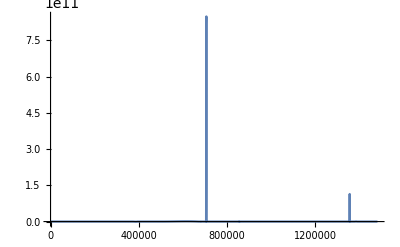

```mathematica
"C:\\Users\\zup98752\\OneDrive - Science and Technology Facilities Council\\CLARA\\RF_Cond_stats\\FINAL_1\\CRP_Data.csv"
FastListPlot[kfpdata0,PlotRange->All]
```

```mathematica
(* we want time vs vac_level *)
pldata=Partition[Flatten[Table[Transpose[{td⟦i,2⟧⟦All,72⟧,td⟦i,2⟧⟦All,15⟧}],{i,1,Length@td}]],2];
pldata0=Transpose[{pldata⟦All,1⟧-pldata⟦1,1⟧,pldata⟦All,2⟧}];
```

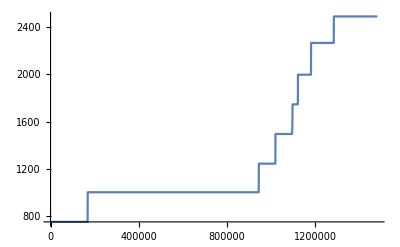

```mathematica
FastListPlot[pldata0,PlotRange->All]
```

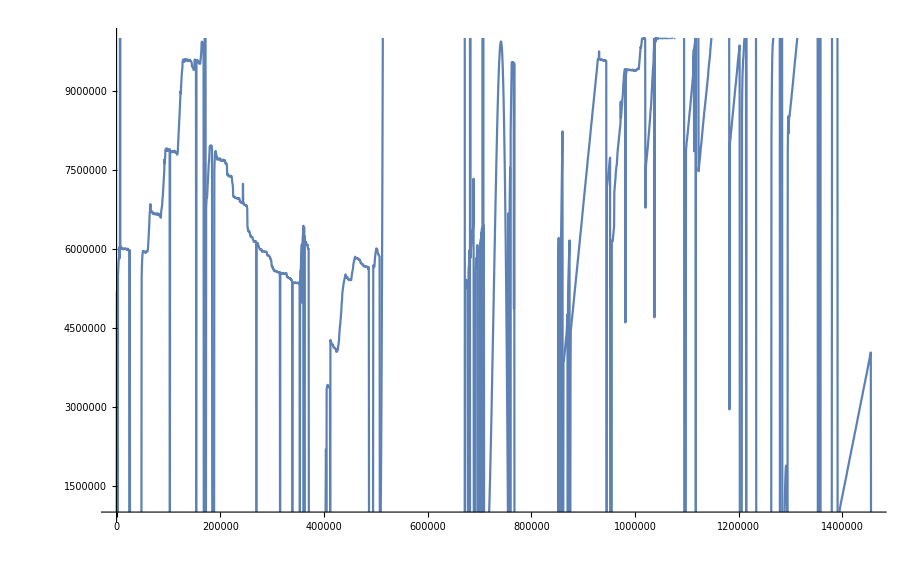

```mathematica
FastListPlot[kfpdata0,PlotRange->{All,{10^6,10^7}}]
```

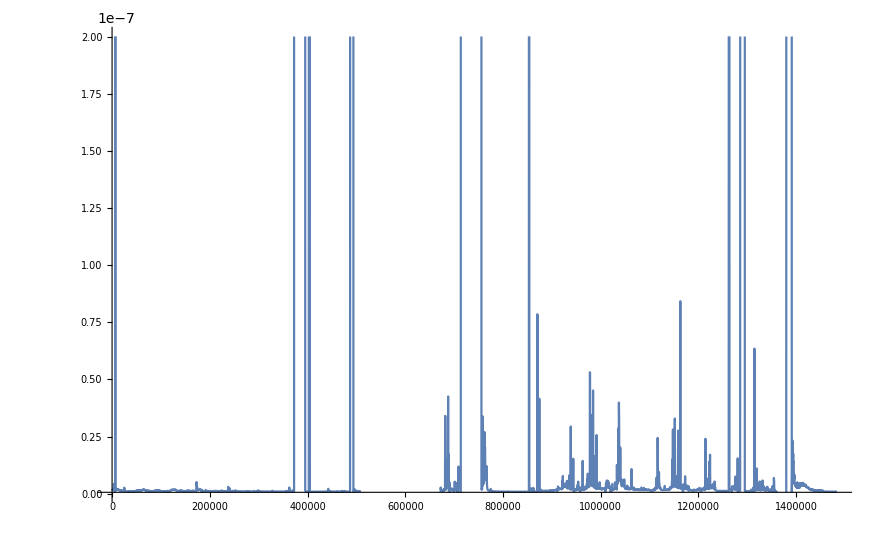

```mathematica
FastListPlot[vacdata0,PlotRange->{All,{6 10^-10,2 10^-7}}]
```

### MultiPlot

```mathematica
ListPlot[vacdata]
```

-Graphics-

```mathematica
dataN=data;
```

```mathematica
P1=ListPlot[dataN⟦All,45⟧,PlotStyle->Blue,ImagePadding->50,Frame->{True,True,True,False},ImageSize->750,FrameStyle->{Automatic,Blue,Automatic,Automatic}];
P2=ListPlot[dataN⟦All,46⟧,PlotStyle->Red,ImagePadding->50,Axes->False,Frame->{False,False,False,True},ImageSize->750,PlotRange->{All,{0,600}},FrameTicks->{{None,All},{None,None}},FrameLabel->{"Time (s)",""},FrameStyle->{Automatic,Automatic,Automatic,Red}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
P3=ListLogPlot[dataN⟦All,39⟧,PlotStyle->Green,ImagePadding->50,Axes->False,Frame->{False,False,False,True},ImageSize->750,PlotRange->{All,{1 10^-10,1 10^-7}},FrameTicks->{{None,All},{None,None}},FrameLabel->{"Time (s)",""},FrameStyle->{Automatic,Automatic,Automatic,Green},Joined->True]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListLogPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

ListLogPlot[Symbol[],PlotStyle→RGBColor[0, 1, 0],ImagePadding→50,Axes→False,Frame→{False,False,False,True},ImageSize→750,PlotRange→{All,{1/10000000000,1/10000000}},FrameTicks→{{None,All},{None,None}},FrameLabel→{Time (s),},FrameStyle→{Automatic,Automatic,Automatic,RGBColor[0, 1, 0]},Joined→True]

## Event pickles

To convert raw power values  to Watts, do value^2/100

```mathematica
init[]:=RegisterExternalEvaluator["Python","C:\\Python36\\python.exe"];(* or path to your python, you also need to "pip install pyzmq"*)
getSortedDataKeys[string_,allkeys_]:=Block[{keys=Select[allkeys,StringContainsQ[#,string]∧StringContainsQ[#,"data"]&]},Sort[Transpose[{ToExpression[StringSplit[keys,"_"]⟦All,-2⟧],keys}]]⟦All,2⟧]
getSortedDataKeys[string_,allkeys_,rawdata_]:=rawdata⟦1⟧[#]&/@getSortedDataKeys[string,allkeys]
```

```mathematica
FastListPlot[data_,opts:OptionsPattern[]]:=Module[{interp},interp=Interpolation[data];
Plot[interp[x],{x,interp[[1,1,1]],interp[[1,1,2]]},opts]]
```

```mathematica
init[];
dir="C:\\Users\\djs56\\GitHub\\Software\\Apps\\RF_Conditioner\\v2\\data_log_reader";
SetDirectory[dir];
file=FileNames["*.pkl"]
```

{src.monitors.vac_monitor_1.pkl}

```mathematica
data=ExternalEvaluate["Python", "import pickle; import sys; sys.path.append('<>dir<>'); f= open('"<>#<>"', 'rb'); data = pickle.load(f); data"] &/@file;
allkeys=Keys[data⟦1⟧];
```

```mathematica
CRpowdata=getSortedDataKeys["CAVITY_REVERSE_POWER",allkeys,data];
KFpowdata=getSortedDataKeys["KLYSTRON_FORWARD_POWER",allkeys,data];
```

```mathematica
ListPlot[crpowdata]
```

-Graphics-

```mathematica
keys=Select[allkeys,StringContainsQ[#,"KLYSTRON_FORWARD_POWER"]∧StringContainsQ[#,"data"]&];
sortedkeys=Sort[Transpose[{ToExpression[StringSplit[keys,"_"]⟦All,-2⟧],keys}]]⟦All,2⟧;
```

```mathematica
krpowdata=data⟦1⟧[#]&/@sortedkeys⟦1;;-1⟧;
```

```mathematica
ListPlot[krpowdata]
```

-Graphics-